# Mixed Postman Tour

## Created Wednesday July 13, 2022

This document contains a condensed set of instructions on how to solve the Mixed Chinese Postman Problem (MCPP), based on the algorithms described in Chapter 4 of Arc Routing: Problems, Methods, and Applications.

https://drive.google.com/file/d/12j-JQUZTTdeC4NXWyFFm3uODFLpAg2wJ/view

## Overview [[Incomplete]]

Our project goal is to implement an algorithm that takes a mixed graph (graph) and produces a list of edges that is an optimal postman tour through that graph. The existing FindPostmanTour function in Mathematica does not support mixed graphs:

FindPostmanTour::ngen: The generalized FindPostmanTour[Graph[<3>, <3>]] is not implemented.

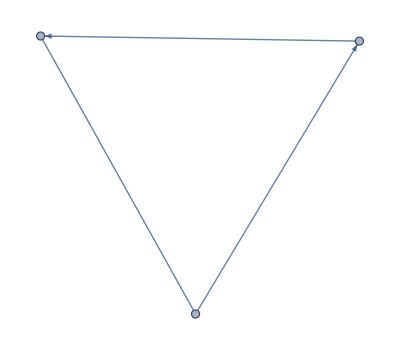
FindPostmanTour[-Graphics-]

```mathematica
FindPostmanTour[Graph[{1<->2,2->3,3->1}]]
```

Chapter 4 of Arc Routing describes a solution to the Mixed Chinese Postman Tour problem. That solution is described by the following points:

If a graph is Eulerian, then Arc Routing states that finding the single tour through that graph is easily computable.

If the graph is not Eulerian, chapter 4 contains

```mathematica
-Graphics--Graphics-
```

```mathematica
-Graphics--Graphics-
```

## Phase 1

## Notes on Book Notation

E — the set of undirected edges

A — the set of directed edges (arcs)

δ^+(S) — the set of directed edges (arcs) that start at S (and are not self loops)

δ^-(S) — the set of directed edges (arcs) that end at S (and are not self loops)

δ(S) — the set of undirected edges with exactly one endpoint at S

δ^*(S) — the union of δ(S), δ^-(S), and δ^+(S); i.e. all directed and undirected edges that start or end at S

x(F) — where F is a subset of edges, the sum of the number of times those links appear in the tour

Let x_e represent the number of times a link e ∈ E ∪ A appears in the tour.

## Implementation

### Install Peter’s paclet

```mathematica
PacletInstall["PeterBurbery/MixedGraphs"]
```

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

### Generate a random mixed graph using Peter’s RandomMixedGraph

### FindMixedPostmanTour

#### Jaebum’s Code

```mathematica
MixedPostmanTour[graph_?GraphQ]:=Block[{
	une,de,
	unX,
	unrevX,
	dX,
	vlist,
	c412,
	elist,
	res,
	edges
},
	une=EdgeList[graph,_UndirectedEdge];
	de=EdgeList[graph,_DirectedEdge];
unX=und@@@une;
unrevX=Reverse/@unX;
	dX=d@@@de;
vlist=VertexList[graph];
Cases[dX, d[1,_]]
]
```

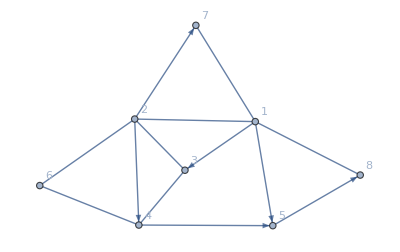

```mathematica
randomGraph=RandomWeightedMixedGraph[BarabasiAlbertGraphDistribution[8,2],0.68,RandomInteger[{1,7}]&,VertexLabels->Automatic]
```

```mathematica
RepeatedTiming@MixedPostmanTour[randomGraph]
```

{0.0000454802,{d[1,3],d[1,5],d[1,2]}}

```mathematica
EdgeList[randomGraph,1->_]
```

{1->3,1->5,1->2}

```mathematica
EdgeList[randomGraph,_->1]
```

{}

```mathematica
Cases[EdgeList[randomGraph,_UndirectedEdge],1<->_]
```

{1<->7,1<->8}

```mathematica
RepeatedTiming@MixedGraphUndirectedEdges[randomGraph]
```

{0.0000147463,{1<->7,1<->8,2<->6,3<->4,4<->6}}

```mathematica
RepeatedTiming@MixedGraphDirectedArcs[randomGraph]
```

{7.99279×10^-6,{1->3,1->5,1->2,2->4,2->3,2->7,4->5,5->8}}

```mathematica
?MixedGraphUndirectedEdges
```

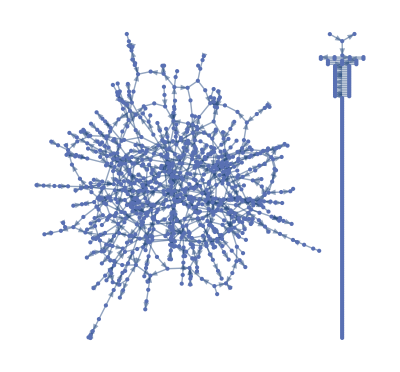

```mathematica
randomLargeGraph=RandomWeightedMixedGraph[BernoulliGraphDistribution[1000,0.002],0.68,RandomInteger[{1,7}]&]
```

```mathematica
First@RepeatedTiming[EdgeList[randomLargeGraph,_UndirectedEdge]]
```

0.000170131

```mathematica
FullForm[Hold@EdgeList[randomLargeGraph,_<->_]]
```

Hold[EdgeList[randomLargeGraph,UndirectedEdge[Blank[],Blank[]]]]

```mathematica
FullForm[Hold@EdgeList[randomLargeGraph,_UndirectedEdge]]
```

Hold[EdgeList[randomLargeGraph,Blank[UndirectedEdge]]]

```mathematica
First@RepeatedTiming[EdgeList[randomLargeGraph,_<->_]]
```

0.000182554

## Undirected Weighted Eulerize

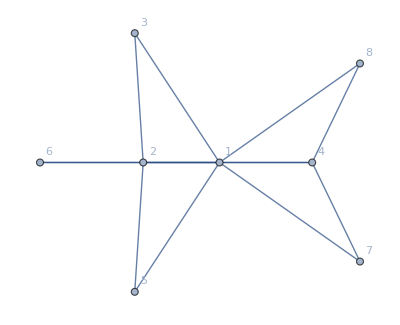

```mathematica
randomGraph=RandomWeightedMixedGraph[BarabasiAlbertGraphDistribution[8,2],0,RandomInteger[{1,7}]&,VertexLabels->Automatic]
```

```mathematica
EdgeList[randomGraph,_<->_]
```

{1<->2,1<->3,1<->4,2<->3,2<->4,2<->8,3<->5,3<->7,4<->5,4<->6,4<->7,5<->6,5<->8}

```mathematica
Subsets[EdgeList[randomGraph,_<->_]]
```

```mathematica
2^EdgeCount[randomGraph]
```

8192

This approach will not work because there are 2^edges edge subsets.

```mathematica
Subsets[OddNodes[randomGraph]]
```

{{},{1},{4},{1,4}}

```mathematica
IncidenceList[randomGraph,1]
```

{1<->2,1<->3,1<->4}

```mathematica
IncidenceList[randomGraph,4]
```

{1<->4,2<->4,4<->5,4<->6,4<->7}

```mathematica
IncidenceMatrix[randomGraph]//MatrixForm
```

(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Prepend[IncidenceMatrix[randomGraph],EdgeList[randomGraph]]//Grid
```

1<->2 | 1<->3 | 1<->4 | 2<->3 | 2<->4 | 2<->8 | 3<->5 | 3<->7 | 4<->5 | 4<->6 | 4<->7 | 5<->6 | 5<->8
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1

```mathematica
TableForm[IncidenceMatrix[randomGraph],TableHeadings->{VertexList[randomGraph],EdgeList[randomGraph]}]
```

| 1<->2 | 1<->3 | 1<->4 | 2<->3 | 2<->4 | 2<->8 | 3<->5 | 3<->7 | 4<->5 | 4<->6 | 4<->7 | 5<->6 | 5<->8
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
4 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
5 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1
6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
8 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1

```mathematica
TableForm[Transpose[IncidenceMatrix[randomGraph]],TableHeadings->{EdgeList[randomGraph],VertexList[randomGraph]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1<->2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1<->3 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1<->4 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
2<->3 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
2<->4 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
2<->8 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
3<->5 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
3<->7 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
4<->5 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
4<->6 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
4<->7 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
5<->6 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
5<->8 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1

```mathematica
Extract[IncidenceMatrix[randomGraph],{{All,1},{All,5}}]
```

{SparseArray[…],SparseArray[…]}

```mathematica
Array[Indexed[x,{##}]&,{10,10}]
```

{{x11,x12,x13,x14,x15,x16,x17,x18,x19,x110},{x21,x22,x23,x24,x25,x26,x27,x28,x29,x210},{x31,x32,x33,x34,x35,x36,x37,x38,x39,x310},{x41,x42,x43,x44,x45,x46,x47,x48,x49,x410},{x51,x52,x53,x54,x55,x56,x57,x58,x59,x510},{x61,x62,x63,x64,x65,x66,x67,x68,x69,x610},{x71,x72,x73,x74,x75,x76,x77,x78,x79,x710},{x81,x82,x83,x84,x85,x86,x87,x88,x89,x810},{x91,x92,x93,x94,x95,x96,x97,x98,x99,x910},{x101,x102,x103,x104,x105,x106,x107,x108,x109,x1010}}

```mathematica
Extract[Array[Indexed[x,{##}]&,{9,9}],{{All,2},{All,5}}]
```

{{x12,x22,x32,x42,x52,x62,x72,x82,x92},{x15,x25,x35,x45,x55,x65,x75,x85,x95}}

```mathematica
MatrixForm/@Extract[IncidenceMatrix[randomGraph],{{All,2},{All,5}}]
```

{(1
0
1
0
0
0
0
0),(0
1
0
1
0
0
0
0)}

## Windy Postman Problem Example

```mathematica
IntegerProgrammingFormulationWindyPostmanProblem[graph_?GraphQ]:=Block[{
	une,de,
	unX,
	unrevX,
	dX,
	vlist,
	c412,
	elist,
	res,
	edges
},une=EdgeList[graph,_UndirectedEdge];
	de=EdgeList[graph,_DirectedEdge];

	unX=und@@@une;
	dX=d@@@de;
	vlist=VertexList[graph];
	unrevX=Reverse/@unX;
	c412=Total[
			Cases[unX, und[#,_]|und[_,#]](*this is a subset of unX*)(*this or with | is for edges like 1 getting 1<->2 and 3<->1*)(*Subscript[x, ij]*)(*I can use IncidenceList for this*)
			-Reverse/@Cases[unX, und[#,_]|und[_,#]](*Subscript[x, ji]*)(*this is a subset of unrevX*)
		]&/@vlist;
elist=Flatten[{unX,unrevX,dX}];
res=LinearOptimization[
		(Total[unX+unrevX]+Total[dX]),
		{
			(*4.11*)
			unX+unrevX\[VectorGreaterEqual]1,

			(*4.12*)(*a.u+b.v\[VectorLessEqual]1,a.v+b.u\[VectorLessEqual]1,*)
			c412==0,

	

			(*4.14*)
			unX\[VectorGreaterEqual]0,
			unrevX\[VectorGreaterEqual]0
		},
		Element[#,Integers]&/@elist];

	edges=Flatten[
		If[#[[2]]>0,Table[#[[1]],{#[[2]]}],Nothing]&/@res
	]/.{und->UndirectedEdge}
	]
```

```mathematica
IntegerProgrammingFormulationWindyPostmanProblem[randomGraph]
```

{1<->3,1<->4,2<->4,2<->8,3<->7,4<->5,5<->6,2<->1,4<->1,3<->2,5<->3,6<->4,7<->4,8<->5}

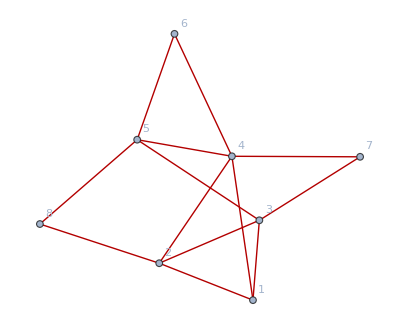

```mathematica
HighlightGraph[randomGraph,IntegerProgrammingFormulationWindyPostmanProblem[randomGraph]]
```

Jaebum’s code does not take edge weights into account.

Attempt to take edge weights into account:

```mathematica
IntegerProgrammingWithWeightsFormulationWindyPostmanProblem[graph_?GraphQ]:=Block[{
	une,de,
	unX,
	unrevX,
	dX,
	vlist,
	c412,
	elist,
	res,
	edges,weights
},une=EdgeList[graph,_UndirectedEdge];
	de=EdgeList[graph,_DirectedEdge];
weights=WeightedAdjacencyMatrix[graph];
	unX=und@@@une;
	dX=d@@@de;
	vlist=VertexList[graph];
	unrevX=Reverse/@unX;
	c412=Total[
			Cases[unX, und[#,_]|und[_,#]](*this is a subset of unX*)(*this or with | is for edges like 1 getting 1<->2 and 3<->1*)(*Subscript[x, ij]*)(*I can use IncidenceList for this*)
			-Reverse/@Cases[unX, und[#,_]|und[_,#]](*Subscript[x, ji]*)(*this is a subset of unrevX*)
		]&/@vlist;
elist=Flatten[{unX,unrevX,dX}];
res=LinearOptimization[
		(Total[unX+unrevX]+Total[dX]),
		{
			(*4.11*)
			unX+unrevX\[VectorGreaterEqual]1,

			(*4.12*)(*a.u+b.v\[VectorLessEqual]1,a.v+b.u\[VectorLessEqual]1,*)
			c412==0,

	

			(*4.14*)
			unX\[VectorGreaterEqual]0,
			unrevX\[VectorGreaterEqual]0
		},
		Element[#,Integers]&/@elist];

	edges=Flatten[
		If[#[[2]]>0,Table[#[[1]],{#[[2]]}],Nothing]&/@res
	]/.{und->UndirectedEdge};Dimensions[unX]
	]
```

```mathematica
IntegerProgrammingWithWeightsFormulationWindyPostmanProblem[randomGraph]
```

LinearOptimization::ubnd: The problem is unbounded.

{5}

```mathematica
EdgeCount[randomGraph]
```

13

```mathematica
Dimensions[WeightedAdjacencyMatrix[randomGraph]]
```

{8,8}

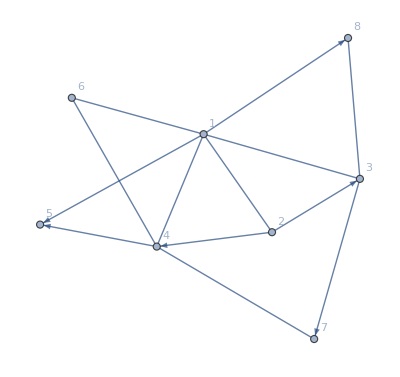

```mathematica
randomGraph=RandomWeightedMixedGraph[BarabasiAlbertGraphDistribution[8,2],0.68,RandomInteger[{1,7}]&,VertexLabels->Automatic]
```

```mathematica
WeightedAdjacencyMatrix[randomGraph]//MatrixForm
```

(0 | 3 | 3 | 1 | 3 | 3 | 0 | 4
3 | 0 | 4 | 5 | 0 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0 | 0 | 6 | 1
0 | 0 | 0 | 0 | 2 | 1 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
WeightedAdjacencyMatrix[randomGraph]
```

SparseArray[…]

```mathematica
UpperTriangularize[WeightedAdjacencyMatrix[randomGraph]]//MatrixForm
```

(0 | 3 | 3 | 1 | 3 | 3 | 0 | 4
0 | 0 | 4 | 5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6 | 1
0 | 0 | 0 | 0 | 2 | 1 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
UpperTriangularize[WeightedAdjacencyMatrix[randomGraph]]
```

SparseArray[…]

```mathematica
Flatten[UpperTriangularize[WeightedAdjacencyMatrix[randomGraph]]]//Normal
```

{0,3,3,1,3,3,0,4,0,0,4,5,0,0,0,0,0,0,0,0,0,0,6,1,0,0,0,0,2,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
DeleteCases[Normal@Flatten[UpperTriangularize[WeightedAdjacencyMatrix[randomGraph]]],0]
```

{3,3,1,3,3,4,4,5,6,1,2,1,2}

## Understanding the Weighted Adjacency Matrix

```mathematica
WeightedAdjacencyMatrix@PetersenGraph[EdgeWeight->{(1<->4->7)}]//MatrixForm
```

(0 | 0 | 1 | 7 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0)

```mathematica
Extract[WeightedAdjacencyMatrix@PetersenGraph[EdgeWeight->{(1<->4->7)}],{{1,4}}]
```

{7}

## Incidence Matrix

```mathematica
TableForm[IncidenceMatrix[PetersenGraph[EdgeWeight->{(1<->4->7)}]],TableHeadings->{VertexList[PetersenGraph[EdgeWeight->{(1<->4->7)}]],EdgeList[PetersenGraph[EdgeWeight->{(1<->4->7)}]]}]
```

| 1<->3 | 1<->4 | 1<->6 | 2<->4 | 2<->5 | 2<->7 | 3<->5 | 3<->8 | 4<->9 | 5<->10 | 6<->7 | 6<->10 | 7<->8 | 8<->9 | 9<->10
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
5 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
6 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
7 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0
9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1

```mathematica
TableForm[Transpose[IncidenceMatrix[PetersenGraph[EdgeWeight->{(1<->4->7)}]]],TableHeadings->{EdgeList[PetersenGraph[EdgeWeight->{(1<->4->7)}]],VertexList[PetersenGraph[EdgeWeight->{(1<->4->7)}]]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1<->3 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1<->4 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1<->6 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
2<->4 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
2<->5 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
2<->7 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
3<->5 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
3<->8 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
4<->9 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
5<->10 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
6<->7 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
6<->10 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
7<->8 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
8<->9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
9<->10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1

```mathematica
WeightedAdjacencyMatrix[PetersenGraph[EdgeWeight->{(1<->4->7)}]].IncidenceMatrix[PetersenGraph[EdgeWeight->{(1<->4->7)}]]
```

SparseArray[…]

```mathematica
WeightedAdjacencyMatrix[PetersenGraph[EdgeWeight->{(1<->4->7)}]].IncidenceMatrix[PetersenGraph[EdgeWeight->{(1<->4->7)}]]//MatrixForm
```

(1 | 7 | 1 | 7 | 0 | 0 | 1 | 1 | 7 | 0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0
7 | 7 | 7 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1
1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1)

```mathematica
TableForm[WeightedAdjacencyMatrix[PetersenGraph[EdgeWeight->{(1<->4->7)}]].IncidenceMatrix[PetersenGraph[EdgeWeight->{(1<->4->7)}]],TableHeadings->{VertexList[PetersenGraph[EdgeWeight->{(1<->4->7)}]],EdgeList[PetersenGraph[EdgeWeight->{(1<->4->7)}]]}]
```

| 1<->3 | 1<->4 | 1<->6 | 2<->4 | 2<->5 | 2<->7 | 3<->5 | 3<->8 | 4<->9 | 5<->10 | 6<->7 | 6<->10 | 7<->8 | 8<->9 | 9<->10
1 | 1 | 7 | 1 | 7 | 0 | 0 | 1 | 1 | 7 | 0 | 1 | 1 | 0 | 0 | 0
2 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
3 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0
4 | 7 | 7 | 7 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
5 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1
6 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1
7 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0
8 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1
9 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
10 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1